Valores inmediatos y diferidos

En Wolfram Language hay dos formas de hacer una asignación: la asignación inmediata (=), y la asignación diferida (:=).

En la asignación inmediata, el valor se calcula tan pronto como se hace la asignación y ya no vuelve a recalcularse. En la diferida, el cálculo del valor se deja pendiente pero se lleva a cabo cada vez que se requiere.

Por ejemplo, considere la distinción entre value=RandomColor[ ] y value:=RandomColor[ ].

En la asignación inmediata (=), se genera inmediatamente un color aleatorio:

```mathematica
value=RandomColor[ ]
```

RGBColor[0.5776360098335713, 0.16742506587239303, 0.23693496006313164]

Y cada vez que se solicita value, se obtiene el mismo color:

```mathematica
value
```

RGBColor[0.5776360098335713, 0.16742506587239303, 0.23693496006313164]

En cambio, en la asignación diferida (:=) no se genera de inmediato el color aleatorio:

```mathematica
value:=RandomColor[ ]
```

Pero cada  vez que se solicita value, se efectúa RandomColor[ ], y se genera nuevamente el color:

```mathematica
value
```

RGBColor[0.8431574152311205, 0.8848301850335125, 0.4749471491092443]

Por lo regular, el color será distinto en cada ocasión:

```mathematica
value
```

RGBColor[0.7127712074377826, 0.37013138983058824, 0.9880717025911983]

Es muy común que se use := si no se tiene ya todo listo al estar definiendo un valor.

Puede hacerse una asignación diferida para círculos aun cuando no se tenga listo el valor de n:

```mathematica
circles:=Graphics[Table[Circle[{x,0},x/2],{x,n}]]
```

Ahora, se le da un valor a n:

```mathematica
n=6
```

6

Entonces, se pide circles y será entonces cuando se usen los valores que se le hayan dado a n:

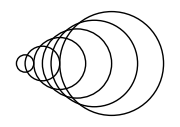

```mathematica
circles
```

La idea de la asignación diferida es directamente análoga al concepto Delayed que se vio en el despliegue de páginas web. En la asignación diferida no se calcula un valor hasta que se necesita. De la misma manera, al usar CloudDeploy con Delayed no se computa el contenido de una página web hasta el momento que alguien la solicita.

Existe también la noción de reglas diferidas. x→rhs calcula inmediatamente rhs. En cambio, en el caso de la regla diferida x:>rhs (escrito como :>), rhs se recalcula cada vez que se solicita.

Aquí se tiene una regla inmediata, donde se calcula inmediatamente un valor específico de RandomReal[ ]:

```mathematica
x->RandomReal[ ]
```

x→0.522293

Se puede hacer la sustitución de cuatro x, pero todas resultan ser iguales:

```mathematica
{x,x,x,x}/.x->RandomReal[ ]
```

{0.821639,0.821639,0.821639,0.821639}

Ahora se tiene una regla diferida, donde el cálculo de RandomReal[ ] se difiere:

```mathematica
x:>RandomReal[ ]
```

x:>RandomReal[ ]

RandomReal[ ] se calcula separadamente cada vez que se hace la sustitución de cada x, lo que resulta en cuatro valores diferentes:

```mathematica
{x,x,x,x}/.x:>RandomReal[ ]
```

{0.536115,0.84214,0.242933,0.514131}

Vocabulario

x:=value |   | asignación diferida, que se evalúa cada vez que se solicita x
x:>value |   | regla diferida, que se evalúa cada vez que se encuentra x (se escribe como :>)

"2 Exercises Available" | "Get Started »"

Sustituya x en {x,x+1,x+2,x^2} por el mismo número aleatorio del 0 al 100. »

| Sample expected output: |  
  | {97,98,99,9409} |

Sustituya cada x en {x,x+1,x+2,x^2} por un número aleatorio del 0 al 100, escogido por separado. »

| Sample expected output: |  
  | {100,3,38,7225} |

Preguntas y respuestas

¿Por qué no usar siempre :=?

Porque no siempre se quiere recalcular algo, a menos que sea necesario. Es más eficiente calcular en una sola ocasión y luego usar el mismo resultado una y otra vez.

¿Cómo se enuncian en voz alta := y :>?

:= se dice, por lo general, “dos puntos igual” aunque, a veces, “asignación diferida”. :> casi siempre “dos puntos mayor” pero, también, “regla diferida”.

¿Qué sucede si se quiere calcular x=x+1, pero x no tiene un valor asignado?

Se inicia un bucle infinito que será interrumpido por el sistema en algún momento. Con x={x} sucede lo mismo.

¿Qué significan las etiquetas In[n]:= para las entradas, y Out[n]= para las salidas ?

Indican que las entradas se asignan a In[n] y las salidas a Out[n]. El := para la entrada significa que la asignación es diferida, de manera tal que si se solicita In[n] se recalcula el resultado.

Notas técnicas

El proceso de computar los resultados en Wolfram Language se llama usualmente evaluación, ya que involucra encontrar el valor de algo.

En Wolfram Language hay distintas formas de controlar la evaluación. Por ejemplo, la función Hold mantiene una expresión “retenida” hasta que se la “libera”.

La forma interna de x=y es Set[x,y]. x:=y es SetDelayed[x,y]. x:>y es RuleDelayed[x,y].